{#,it,t,i,rho,vx,P,px,Etot}

{1,1,1,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999999,0.999999,0.999998,0.999996,0.999994,0.999992,0.999987,0.999981,0.999972,0.99996,0.999942,0.999917,0.999883,0.999836,0.999772,0.999687,0.999574,0.999427,0.999236,0.998992,0.998682,0.998295,0.997815,0.997226,0.996513,0.995656,0.994639,0.993443,0.992049,0.990443,0.988609,0.98653,0.984198,0.9816,0.978731,0.975583,0.972157,0.96845,0.964464,0.960202,0.955672,0.950879,0.945831,0.940537,0.935008,0.929255,0.923286,0.917113,0.910748,0.904202,0.897482,0.890602,0.88357,0.876396,0.869088,0.861654,0.854103,0.846443,0.83868,0.830819,0.82287,0.814835,0.806721,0.798532,0.790272,0.781948,0.773561,0.765115,0.756613,0.74806,0.739457,0.730806,0.722111,0.713373,0.704595,0.695776,0.686921,0.678031,0.669105,0.660147,0.651156,0.642134,0.633082,0.623999,0.61489,0.605752,0.596587,0.587395,0.578177,0.568933,0.559664,0.55037,0.541051,0.531708,0.52234,0.512949,0.503533,0.494093,0.484631,0.475144,0.465635,0.456101,0.446545,0.436965,0.427362,0.417735,0.408085,0.398412,0.388714,0.378994,0.36925,0.359482,0.349691,0.339876,0.330037,0.320173,0.310286,0.300375,0.29044,0.28048,0.270497,0.260489,0.250458,0.240402,0.230321,0.220217,0.210089,0.199937,0.189762,0.179563,0.169341,0.159097,0.14883,0.13854,0.128231,0.1179,0.10755,0.097182,0.0867972,0.0763965,0.0659819,0.055557,0.0451226,0.0346847,0.0242449,0.013811,0.00338791,-0.00701493,-0.0173869,-0.0277143,-0.037978,-0.0481545,-0.0582109,-0.0681007,-0.0777644,-0.0871154,-0.0960299,-0.104344,-0.111829,-0.118202,-0.123161,-0.126491,-0.128238,-0.128803,-0.128779,-0.128604,-0.12844,-0.128301,-0.128181,-0.128073,-0.127978,-0.127892,-0.127814,-0.127744,-0.12768,-0.127623,-0.127571,-0.127523,-0.12748,-0.12744,-0.127405,-0.127373,-0.127342,-0.127316,-0.12729,-0.127267,-0.127247,-0.127228,-0.12721,-0.127195,-0.127181,-0.127166,-0.127155,-0.127144,-0.127134,-0.127124,-0.127116,-0.127108,-0.127101,-0.127093,-0.127088,-0.127082,-0.127077,-0.127071,-0.127067,-0.127063,-0.127059,-0.127055,-0.127052,-0.127049,-0.127046,-0.127044,-0.127041,-0.127038,-0.127036,-0.127035,-0.127032,-0.127031,-0.12703,-0.127028,-0.127026,-0.127025,-0.127024,-0.127023,-0.127021,-0.127021,-0.127019,-0.127019,-0.127017,-0.127017,-0.127015,-0.127015,-0.127015,-0.127013,-0.127013,-0.127012,-0.127012,-0.127012,-0.12701,-0.12701,-0.12701,-0.127009,-0.127009,-0.127009,-0.127008,-0.127008,-0.127008,-0.127007,-0.127007,-0.127007,-0.127008,-0.127007,-0.127007,-0.127007,-0.127006,-0.127006,-0.127007,-0.127007,-0.127006,-0.127006,-0.127006,-0.127007,-0.127006,-0.127006,-0.127007,-0.127007,-0.127007,-0.127007,-0.127007,-0.127007,-0.127008,-0.127007,-0.127008,-0.127008,-0.127009,-0.127008,-0.127009,-0.127009,-0.12701,-0.127009,-0.12701,-0.12701,-0.12701,-0.127009,-0.12701,-0.127011,-0.12701,-0.127011,-0.127012,-0.127012,-0.127012,-0.127013,-0.127013,-0.127014,-0.127015,-0.127015,-0.127016,-0.127017,-0.127017,-0.127017,-0.127017,-0.127018,-0.127018,-0.12702,-0.12702,-0.127021,-0.127022,-0.127023,-0.127024,-0.127025,-0.127026,-0.127026,-0.127028,-0.127029,-0.127031,-0.127032,-0.127032,-0.127035,-0.127037,-0.127039,-0.12704,-0.127041,-0.127043,-0.127044,-0.127046,-0.127045,-0.12704,-0.127026,-0.12699,-0.126904,-0.126706,-0.126247,-0.1252,-0.122822,-0.117463,-0.105591,-0.0802909,-0.0312425,0.0424031,0.100296,0.109356,0.103658,0.100978,0.100238,0.100057,0.100013,0.100003,0.100001,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}

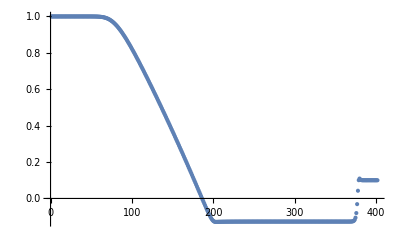

```mathematica
dir=NotebookDirectory[];
data=Import[dir<>"output.dat"];
len=Length[data];
Print[data[[1]]]
data=data[[2;;len,All]];
data=Delete[data,Position[data,{}]];
t0=0.25;
pos=Flatten@Position[data[[All,2]],0.25];
data=data[[pos]];

ϵ=data[[All,8]]-1/2 data[[All,5]]^2
ListPlot[ϵ
,PlotRange->Full
,AxesOrigin->{0,0}]
```

```mathematica
data[[All,8]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.999999,0.999999,0.999999,0.999998,0.999996,0.999994,0.999992,0.999987,0.999981,0.999972,0.99996,0.999942,0.999917,0.999883,0.999836,0.999772,0.999687,0.999574,0.999427,0.999236,0.998992,0.998683,0.998296,0.997817,0.997229,0.996517,0.995663,0.994649,0.993458,0.992072,0.990476,0.988655,0.986595,0.984287,0.981721,0.978893,0.975797,0.972435,0.968807,0.964917,0.960771,0.956378,0.951746,0.946886,0.941809,0.936529,0.931058,0.925408,0.919592,0.913624,0.907517,0.901282,0.894932,0.888478,0.881931,0.875301,0.868597,0.86183,0.855008,0.848139,0.841229,0.834288,0.827319,0.820331,0.813328,0.806315,0.799298,0.79228,0.785266,0.778259,0.771263,0.764281,0.757316,0.75037,0.743446,0.736547,0.729673,0.722828,0.716013,0.709229,0.702478,0.695761,0.68908,0.682435,0.675827,0.669259,0.662729,0.656239,0.64979,0.643383,0.637017,0.630694,0.624413,0.618176,0.611982,0.605832,0.599726,0.593664,0.587647,0.581675,0.575747,0.569865,0.564027,0.558235,0.552488,0.546786,0.541129,0.535518,0.529952,0.52443,0.518954,0.513523,0.508137,0.502796,0.4975,0.492249,0.487042,0.481879,0.476761,0.471688,0.466658,0.461673,0.456731,0.451834,0.44698,0.442169,0.437402,0.432679,0.427999,0.423362,0.418768,0.414217,0.40971,0.405245,0.400823,0.396445,0.392109,0.387817,0.383568,0.379363,0.375202,0.371085,0.367014,0.362987,0.359008,0.355075,0.351192,0.34736,0.343581,0.339858,0.336196,0.332599,0.329075,0.325633,0.322287,0.319054,0.31596,0.313042,0.310347,0.307943,0.305913,0.304343,0.303294,0.302746,0.302569,0.302576,0.302631,0.302683,0.302726,0.302764,0.302798,0.302828,0.302855,0.30288,0.302902,0.302922,0.30294,0.302956,0.302972,0.302985,0.302998,0.303009,0.303019,0.303029,0.303037,0.303045,0.303053,0.303059,0.303065,0.303071,0.303076,0.30308,0.303085,0.303089,0.303092,0.303095,0.303099,0.303101,0.303104,0.303106,0.303109,0.303111,0.303113,0.303114,0.303116,0.303118,0.303119,0.30312,0.303122,0.303123,0.303124,0.303125,0.303126,0.303127,0.303128,0.303129,0.303129,0.30313,0.303131,0.303131,0.303132,0.303133,0.303133,0.303134,0.303134,0.303135,0.303135,0.303136,0.303136,0.303137,0.303137,0.303138,0.303138,0.303138,0.303139,0.303139,0.30314,0.30314,0.30314,0.303141,0.303141,0.303141,0.303142,0.303142,0.303142,0.303143,0.303143,0.303143,0.303144,0.303144,0.303144,0.303144,0.303145,0.303145,0.303145,0.303146,0.303146,0.303146,0.303146,0.303147,0.303147,0.303147,0.303147,0.303148,0.303148,0.303148,0.303148,0.303148,0.303149,0.303149,0.303149,0.303149,0.30315,0.30315,0.30315,0.30315,0.303151,0.303151,0.303151,0.303151,0.303152,0.303152,0.303152,0.303152,0.303153,0.303153,0.303153,0.303154,0.303154,0.303154,0.303155,0.303155,0.303155,0.303156,0.303156,0.303156,0.303157,0.303157,0.303157,0.303158,0.303158,0.303159,0.303159,0.30316,0.30316,0.303161,0.303161,0.303162,0.303162,0.303163,0.303163,0.303164,0.303165,0.303165,0.303166,0.303167,0.303168,0.303169,0.303169,0.30317,0.303171,0.303173,0.303174,0.303175,0.303176,0.303176,0.303176,0.303173,0.303165,0.303145,0.303096,0.302983,0.302723,0.30213,0.300779,0.297733,0.290964,0.27642,0.247479,0.199786,0.147511,0.115644,0.104133,0.101007,0.10024,0.100057,0.100013,0.100003,0.100001,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1}